# Kolokvij (računalniški praktikum)

## 14. januar 2020

## Navodila

Naloge rešujte samostojno. Uporabljati smete svoje zapiske, dokumentacijo za Mathematico in gradivo na internetu.

Če kaj ni jasno, vprašajte asistentko ali asistenta.

Pri vsaki nalogi rešitve zapišite v razdelek “Rešitve”. Rešitve opremite z dovolj besedila, da bomo razumeli vašo resitev. Na primer, če je vprašanje “Izračunajte vrednost y, pri kateri ...”, potem mora biti iz vaše rešitve jasno razvidno, katero vrednost y ste izračunali.

Rešitev ne računajte na roko na papirju, ampak z Mathematico, saj je bistvo preverjanja vaše znanje Mathematice.

Ročno kopiranje rezultatov iz enega računa v naslednjega kaže na slab stil. Za polno število točk naj bodo rešitve napisane tako, da uporabniku ni treba ničesar kopirati ali prepisovati na roko. (Seveda pa morate na roko skopirati vhodne podatke iz besedila naloge.)

## 1. naloga

Naloga 1.1: Numerično na 10 mest natančno izračunajte vrednost izraza (95 x^7)/(323-107·3)^8 pri x=1,…,10.

Naloga 1.2: Poiščite trimestno število, deljivo z 19, katerega tretja števka je vsota prvih dveh.

Naloga 1.3: Dano je zaporedje a_n=k+3n. Pri kateri vrednosti celoštevilskega parametra k je vsota prvih k členov zaporedja enaka 837 ?

### Rešitve

#### Prva podnaloga

```mathematica
Table[{x, N[95x^7/(323-107*3)^8,10]},{x,1,10}]//TableForm
```

1 | 0.37109375
2 | 47.5
3 | 811.5820313
4 | 6080.
5 | 28991.69922
6 | 103882.5
7 | 305611.6602
8 | 778240.
9 | 1.774929902×10^6
10 | 3.7109375×10^6

#### Druga podnaloga

```mathematica
x/.Solve[x==19*n&&x==100a+10b+c&&a<10&&b<10&&c<10&&c==a+b,x,NonNegativeIntegers][[2]]
```

ConditionalExpression[437,a==4&&b==3&&c==7&&n==23]

#### Tretja podnaloga

```mathematica
k/.Solve[Sum[k+3n,{n,1,k}]==837,k,NonNegativeIntegers]
```

{18}

## 2. naloga

Naloga 2.1:  Dan je polinom sin^5 x + sin^4 x+sin^3 x + sin^2 x  v spremenljivki  sin x. Koliko je vrednost polinoma pri x = π/4 ? Razstavi polinom na linearne in kvadratne faktorje.

Naloga 2.2:  Izračunaj prvih 10 odvodov tega polinoma. Pomagaj si s Table. Nato seštej vrednosti vseh izračunanih odvodov v točki x=0.

Naloga 2.3: Nariši graf parametrično podane funkcije: x=27/14 sin(2t)+15/14 sin(3t),  y=27/14 cos(2t)-15/14 cos(3t)  za t∈[0,2π].

Naloga 2.4:   Nariši graf implicitno podane funkcije: sin(x+y)-cos(x y) + 1 = 0 na območju [-5,5]×[-5,5].

### Rešitve

#### Prva podnaloga

```mathematica
polinom[x_]:=Sin[x]^5 + Sin[x]^4 +Sin[x]^3 +Sin[x]^2
polinom[Pi/4]
```

3/4+3/(4 √2)

```mathematica
Factor[polinom[x]]
```

Sin[x]^2 (1+Sin[x]) (1+Sin[x]^2)

#### Druga podnaloga

```mathematica
odvodi = Table[D[polinom[x],{x,n}],{n,1,10}];
odvodi //TableForm
```

2 Cos[x] Sin[x]+3 Cos[x] Sin[x]^2+4 Cos[x] Sin[x]^3+5 Cos[x] Sin[x]^4
2 Cos[x]^2+6 Cos[x]^2 Sin[x]-2 Sin[x]^2+12 Cos[x]^2 Sin[x]^2-3 Sin[x]^3+20 Cos[x]^2 Sin[x]^3-4 Sin[x]^4-5 Sin[x]^5
6 Cos[x]^3-8 Cos[x] Sin[x]+24 Cos[x]^3 Sin[x]-21 Cos[x] Sin[x]^2+60 Cos[x]^3 Sin[x]^2-40 Cos[x] Sin[x]^3-65 Cos[x] Sin[x]^4
-8 Cos[x]^2+24 Cos[x]^4-60 Cos[x]^2 Sin[x]+120 Cos[x]^4 Sin[x]+8 Sin[x]^2-192 Cos[x]^2 Sin[x]^2+21 Sin[x]^3-440 Cos[x]^2 Sin[x]^3+40 Sin[x]^4+65 Sin[x]^5
-60 Cos[x]^3+120 Cos[x]^5+32 Cos[x] Sin[x]-480 Cos[x]^3 Sin[x]+183 Cos[x] Sin[x]^2-1800 Cos[x]^3 Sin[x]^2+544 Cos[x] Sin[x]^3+1205 Cos[x] Sin[x]^4
32 Cos[x]^2-480 Cos[x]^4+546 Cos[x]^2 Sin[x]-4200 Cos[x]^4 Sin[x]-32 Sin[x]^2+3072 Cos[x]^2 Sin[x]^2-183 Sin[x]^3+10220 Cos[x]^2 Sin[x]^3-544 Sin[x]^4-1205 Sin[x]^5
546 Cos[x]^3-4200 Cos[x]^5-128 Cos[x] Sin[x]+8064 Cos[x]^3 Sin[x]-1641 Cos[x] Sin[x]^2+47460 Cos[x]^3 Sin[x]^2-8320 Cos[x] Sin[x]^3-26465 Cos[x] Sin[x]^4
-128 Cos[x]^2+8064 Cos[x]^4-4920 Cos[x]^2 Sin[x]+115920 Cos[x]^4 Sin[x]+128 Sin[x]^2-49152 Cos[x]^2 Sin[x]^2+1641 Sin[x]^3-248240 Cos[x]^2 Sin[x]^3+8320 Sin[x]^4+26465 Sin[x]^5
-4920 Cos[x]^3+115920 Cos[x]^5+512 Cos[x] Sin[x]-130560 Cos[x]^3 Sin[x]+14763 Cos[x] Sin[x]^2-1208400 Cos[x]^3 Sin[x]^2+131584 Cos[x] Sin[x]^3+628805 Cos[x] Sin[x]^4
512 Cos[x]^2-130560 Cos[x]^4+44286 Cos[x]^2 Sin[x]-2996400 Cos[x]^4 Sin[x]-512 Sin[x]^2+786432 Cos[x]^2 Sin[x]^2-14763 Sin[x]^3+6140420 Cos[x]^2 Sin[x]^3-131584 Sin[x]^4-628805 Sin[x]^5

```mathematica
Sum[odvodi[[n]]/.x->0, {n,1,10}]
```

-15130

#### Tretja podnaloga

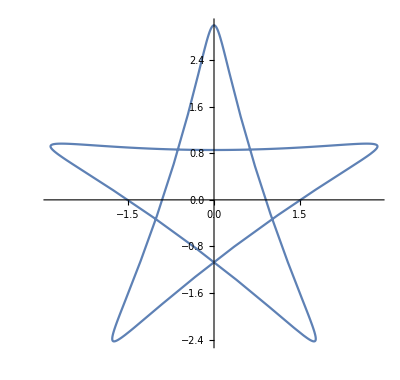

```mathematica
ParametricPlot[{Sin[2t]27/14 + Sin[3t]15/14, Cos[2t]27/14 -Cos[3t]15/14},{t,0,2Pi}]
```

#### Četrta podnaloga

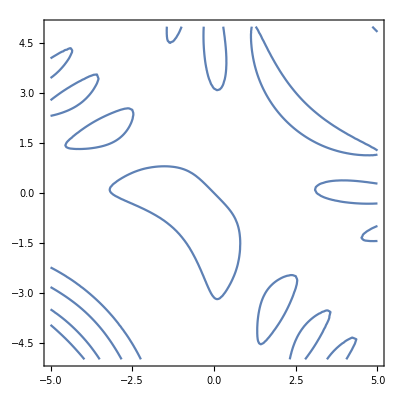

```mathematica
ContourPlot[Sin[x+y]-Cos[x*y]+1==0,{x,-5,5},{y,-5,5}]
```

## 3. naloga

Naloga 3.1:  Dani sta funkciji x^4 in e^x+p. Narišite graf funkcij tako, da boste lahko spreminjali vrednosti p od 0 do 4. Območje risanja omejite na [-2,2]×[0,10].

Naloga 3.2 : Izračunajte ploščino območja med funkcijama za p=2. Namig: Za izračun presečišč si pomagajte s funkcijo FindRoot in izračunajte vsako presečišče posebej.

Naloga 3.3 : Sestavi funkcijo, ki za dano naravno število izračuna število njegovih podvojenih prafaktorjev. Primer: število  360=2·2·2·3·3·5  ima 3 podvojene prafaktorje (dve dvojki in eno trojko). Namig: Razcepi število in seštej eksponente prafaktorjev, zmanjšane za 1. Pomagaj si s funkcijo Total. Tabeliraj vrednosti funkcije za naravna števila do vključno 128.

Naloga 3.4 : Sestavi tabelo števil med 2 in 200, ki nimajo podvojenih prafaktorjev in niso praštevila. Pomagaj si s funkcijama And in Not.

### Rešitve

#### Prva podnaloga

```mathematica
Manipulate[
Plot[{x^4,Exp[x]+p},{x,-2,2},PlotRange->{0,10}],
{p,0,4}
]
```

#### Druga podnaloga

```mathematica
presecisce1 = x/.FindRoot[x^4==Exp[x]+2,{x,-2}]
presecisce2 = x/.FindRoot[x^4==Exp[x]+2,{x,2}]
```

-1.23044

1.63365

```mathematica
ploscina = Integrate[Exp[x]+2-x^4,{x,presecisce1,presecisce2}]
```

7.66733

#### Tretja podnaloga

```mathematica
podvojeno[x_]:=Sum[factor[[2]]-1,{factor,FactorInteger[x]}]
Table[{n,podvojeno[n]},{n,1,128}]//TableForm
```

1 | 0
2 | 0
3 | 0
4 | 1
5 | 0
6 | 0
7 | 0
8 | 2
9 | 1
10 | 0
11 | 0
12 | 1
13 | 0
14 | 0
15 | 0
16 | 3
17 | 0
18 | 1
19 | 0
20 | 1
21 | 0
22 | 0
23 | 0
24 | 2
25 | 1
26 | 0
27 | 2
28 | 1
29 | 0
30 | 0
31 | 0
32 | 4
33 | 0
34 | 0
35 | 0
36 | 2
37 | 0
38 | 0
39 | 0
40 | 2
41 | 0
42 | 0
43 | 0
44 | 1
45 | 1
46 | 0
47 | 0
48 | 3
49 | 1
50 | 1
51 | 0
52 | 1
53 | 0
54 | 2
55 | 0
56 | 2
57 | 0
58 | 0
59 | 0
60 | 1
61 | 0
62 | 0
63 | 1
64 | 5
65 | 0
66 | 0
67 | 0
68 | 1
69 | 0
70 | 0
71 | 0
72 | 3
73 | 0
74 | 0
75 | 1
76 | 1
77 | 0
78 | 0
79 | 0
80 | 3
81 | 3
82 | 0
83 | 0
84 | 1
85 | 0
86 | 0
87 | 0
88 | 2
89 | 0
90 | 1
91 | 0
92 | 1
93 | 0
94 | 0
95 | 0
96 | 4
97 | 0
98 | 1
99 | 1
100 | 2
101 | 0
102 | 0
103 | 0
104 | 2
105 | 0
106 | 0
107 | 0
108 | 3
109 | 0
110 | 0
111 | 0
112 | 3
113 | 0
114 | 0
115 | 0
116 | 1
117 | 1
118 | 0
119 | 0
120 | 2
121 | 1
122 | 0
123 | 0
124 | 1
125 | 2
126 | 1
127 | 0
128 | 6

#### Četrta podnaloga

```mathematica
Select[Range[2,200],podvojeno[#]==0 &&Not[PrimeQ[#]]&]
```

{6,10,14,15,21,22,26,30,33,34,35,38,39,42,46,51,55,57,58,62,65,66,69,70,74,77,78,82,85,86,87,91,93,94,95,102,105,106,110,111,114,115,118,119,122,123,129,130,133,134,138,141,142,143,145,146,154,155,158,159,161,165,166,170,174,177,178,182,183,185,186,187,190,194,195}